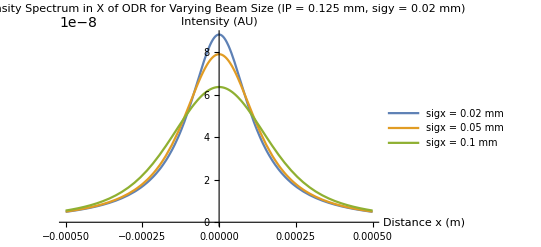

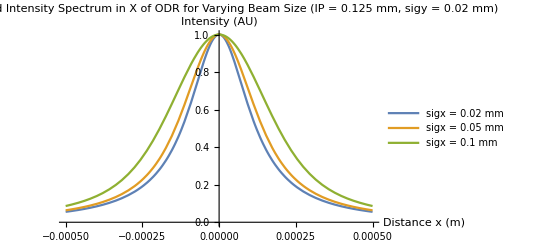

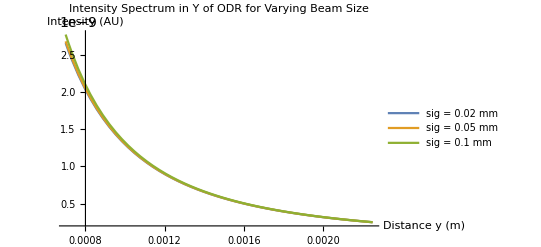

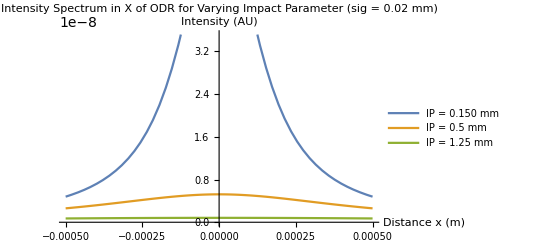

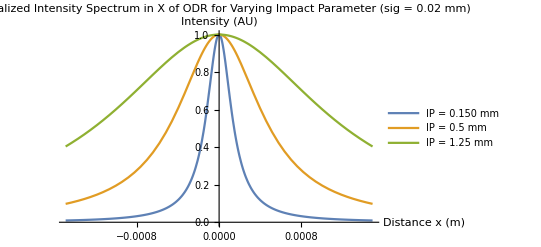

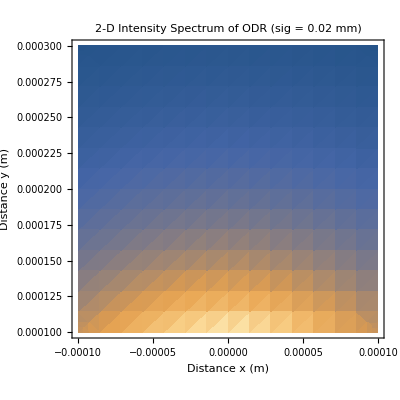

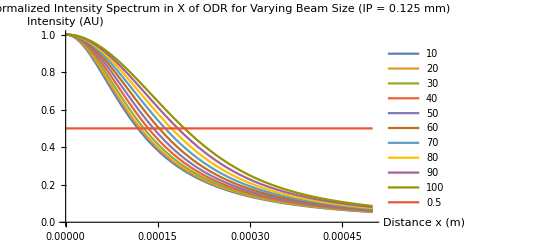

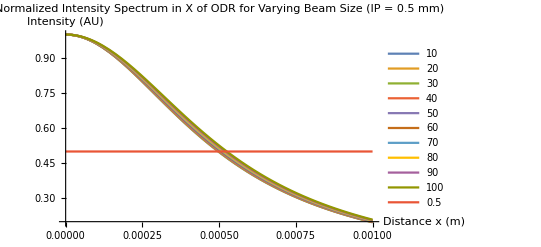

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

Intensity1[ux_,uy_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^2)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{lambda,lowerlambda,upperlambda},PrecisionGoal->6]

Intensity2[ux_,uy_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},PrecisionGoal->6]

HalfWidth[uy_,lambda_,sigx_,sigy_]:=
2*FindRoot[Max[Intensity2[0,uy,lambda,sigx,sigy]]/2-Intensity1[ux,uy,sigx,sigy],{ux,sigx/100}]



Plot[{Intensity2[ux,125*^-6,averagelambda,20*^-6,20*^-6],Intensity2[ux,125*^-6,averagelambda,50*^-6,20*^-6],Intensity2[ux,125*^-6,averagelambda,100*^-6,20*^-6]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.125 mm, sigy = 0.02 mm)",PlotLegends->{"sigx = 0.02 mm","sigx = 0.05 mm","sigx = 0.1 mm"}]
Plot[{Intensity2[ux,125*^-6,averagelambda,20*^-6,20*^-6]/Intensity2[0,125*^-6,averagelambda,20*^-6,20*^-6],Intensity2[ux,125*^-6,averagelambda,50*^-6,20*^-6]/Intensity2[0,125*^-6,averagelambda,50*^-6,20*^-6],Intensity2[ux,125*^-6,averagelambda,100*^-6,20*^-6]/Intensity2[0,125*^-6,averagelambda,100*^-6,20*^-6]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.125 mm, sigy = 0.02 mm)",PlotLegends->{"sigx = 0.02 mm","sigx = 0.05 mm","sigx = 0.1 mm"}]
Plot[{Intensity2[0,uy,averagelambda,20*^-6,20*^-6],Intensity2[0,uy,averagelambda,50*^-6,50*^-6],Intensity2[0,uy,averagelambda,100*^-6,100*^-6]},{uy,700*^-6,2250*^-6},AxesLabel-> {"Distance y (m)","Intensity (AU)"},PlotLabel->"Intensity Spectrum in Y of ODR for Varying Beam Size",PlotLegends->{"sig = 0.02 mm","sig = 0.05 mm","sig = 0.1 mm"}]
Plot[{Intensity2[ux,150*^-6,averagelambda,sigx,sigy],Intensity2[ux,500*^-6,averagelambda,sigx,sigy],Intensity2[ux,1250*^-6,averagelambda,sigx,sigy]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Intensity Spectrum in X of ODR for Varying Impact Parameter (sig = 0.02 mm)",PlotLegends->{"IP = 0.150 mm","IP = 0.5 mm","IP = 1.25 mm"}]
Plot[{Intensity2[ux,150*^-6,averagelambda,sigx,sigy]/Intensity2[0,150*^-6,averagelambda,sigx,sigy],Intensity2[ux,500*^-6,averagelambda,sigx,sigy]/Intensity2[0,500*^-6,averagelambda,sigx,sigy],Intensity2[ux,1250*^-6,averagelambda,sigx,sigy]/Intensity2[0,1250*^-6,averagelambda,sigx,sigy]},{ux,-1500*^-6,1500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Impact Parameter (sig = 0.02 mm)",PlotLegends->{"IP = 0.150 mm","IP = 0.5 mm","IP = 1.25 mm"}]


DensityPlot[Intensity2[ux,uy,averagelambda,sigx,sigy],{ux,-100*^-6,100*^-6},{uy,100*^-6,300*^-6},AxesLabel-> {"Distance x (m)","Distance y (m)"},PlotLabel->"2-D Intensity Spectrum of ODR (sig = 0.02 mm)"]

Plot[{Intensity2[ux,125*^-6,averagelambda,10*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,10*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,20*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,20*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,30*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,30*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,40*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,40*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,50*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,50*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,60*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,60*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,70*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,70*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,80*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,80*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,90*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,90*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,100*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,100*^-6,sigy],0.5},{ux,0,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.125 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]

Plot[{Intensity2[ux,500*^-6,averagelambda,10*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,10*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,20*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,20*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,30*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,30*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,40*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,40*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,50*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,50*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,60*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,60*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,70*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,70*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,80*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,80*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,90*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,90*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,100*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,100*^-6,sigy],0.5},{ux,0,1000*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.5 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]
```

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

IntensityX[ux_,a_,uymax_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{uy,a,uymax},PrecisionGoal->6]
IntensityY[uxwidth_,uy_,lambda_,sigx_,sigy_] :=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{ux,-uxwidth,uxwidth},PrecisionGoal->6]
IntensityTotal[uxwidth_,a_,uymax_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{lambda,lowerlambda,upperlambda},{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{ux,-uxwidth,uxwidth},{uy,a,uymax},PrecisionGoal->6]


Plot[{IntensityX[ux,125*^-6,0.005,averagelambda,20*^-6,20*^-6],IntensityX[ux,125*^-6,0.005,averagelambda,50*^-6,20*^-6],IntensityX[ux,125*^-6,0.005,averagelambda,100*^-6,20*^-6]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->Style["Projected X Intensity Spectrum of ODR for Varying Beam Size (IP = 0.125 mm, sigy = 0.02 mm)",FontSize->18],PlotLegends->Placed[{"sigx = 0.02 mm","sigx = 0.05 mm","sigx = 0.1 mm"},{Center,Right}]]
Plot[{IntensityX[ux,125*^-6,0.005,averagelambda,20*^-6,20*^-6]/IntensityX[0,125*^-6,0.005,averagelambda,20*^-6,20*^-6],IntensityX[ux,125*^-6,0.005,averagelambda,50*^-6,20*^-6]/IntensityX[0,125*^-6,0.005,averagelambda,50*^-6,20*^-6],IntensityX[ux,125*^-6,0.005,averagelambda,100*^-6,20*^-6]/IntensityX[0,125*^-6,0.005,averagelambda,100*^-6,20*^-6]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->Style["Normalized Projected X Intensity Spectrum of ODR for Varying Beam Size (IP = 0.125 mm, sigy = 0.02 mm)",FontSize->18],PlotLegends->Placed[{"sigx = 0.02 mm","sigx = 0.05 mm","sigx = 0.1 mm"},{Center,Right}]]
Plot[{IntensityY[0.005,uy,averagelambda,20*^-6,20*^-6],IntensityY[0.005,uy,averagelambda,50*^-6,50*^-6],IntensityY[0.005,uy,averagelambda,100*^-6,100*^-6]},{uy,700*^-6,2250*^-6},AxesLabel-> {"Distance y (m)","Intensity (AU)"},PlotLabel->Style["Projected Y Intensity Spectrum of ODR for Varying Beam Size",FontSize->18],PlotLegends->Placed[{"sig = 0.02 mm","sig = 0.05 mm","sig = 0.1 mm"},{Center,Right}]]
Plot[{IntensityX[ux,150*^-6,0.005,averagelambda,sigx,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,sigx,sigy],IntensityX[ux,1250*^-6,0.005,averagelambda,sigx,sigy]},{ux,-500*^-6,500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->Style["Projected X Intensity Spectrum of ODR for Varying Impact Parameter (sig = 0.02 mm)",FontSize->18],PlotLegends->Placed[{"IP = 0.150 mm","IP = 0.5 mm","IP = 1.25 mm"},{Center,Right}]]
Plot[{IntensityX[ux,150*^-6,0.005,averagelambda,sigx,sigy]/IntensityX[0,150*^-6,0.005,averagelambda,sigx,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,sigx,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,sigx,sigy],IntensityX[ux,1250*^-6,0.005,averagelambda,sigx,sigy]/IntensityX[0,1250*^-6,0.005,averagelambda,sigx,sigy]},{ux,-1500*^-6,1500*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->Style["Normalized Projected X Intensity Spectrum of ODR for Varying Impact Parameter (sig = 0.02 mm)",FontSize->18],PlotLegends->Placed[{"IP = 0.150 mm","IP = 0.5 mm","IP = 1.25 mm"},{Center,Right}]]


1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.00001,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.00002,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.00005,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.0001,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.0002,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.0005,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.001,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.002,0.01,sigx,sigy]
1/(4*Pi*eps0)*averagelambda/(hbar*2*Pi*c)*1/n*IntensityTotal[0.005,0.005,0.01,sigx,sigy]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

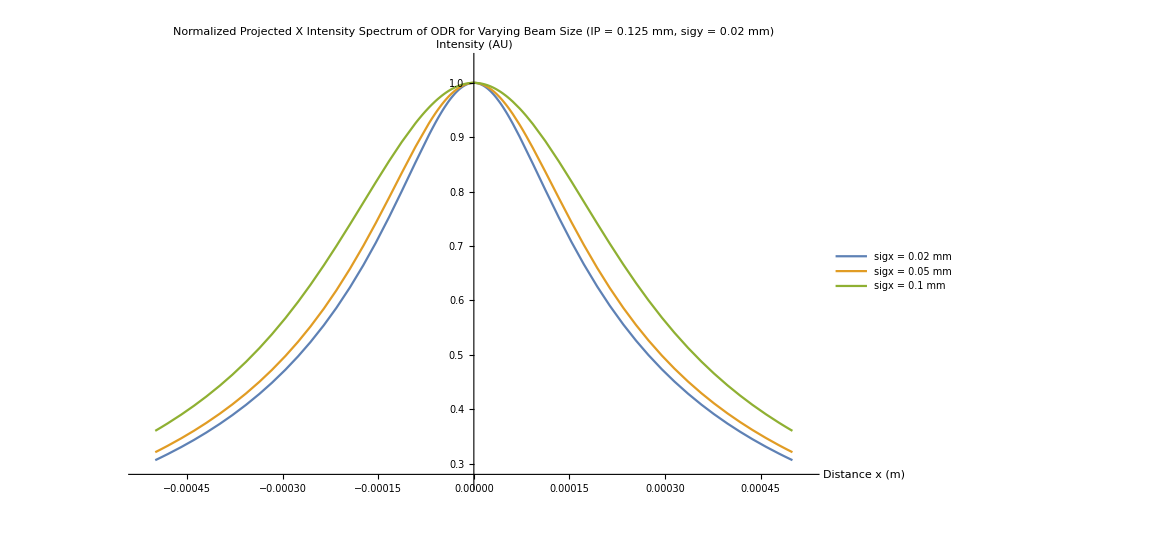

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

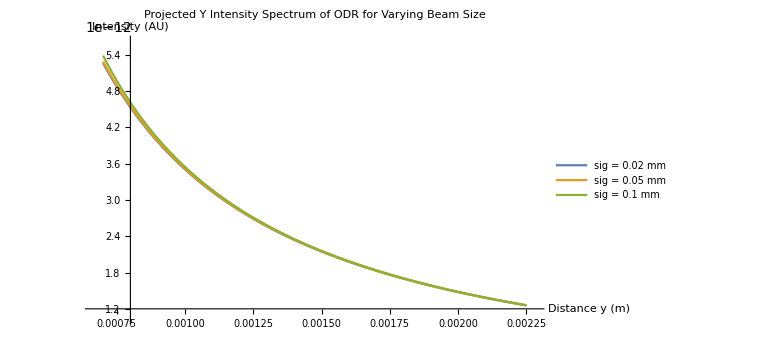

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

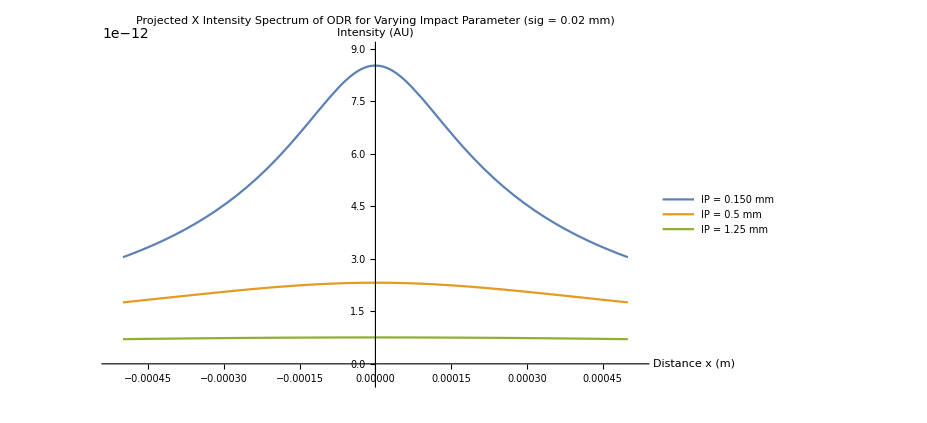

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

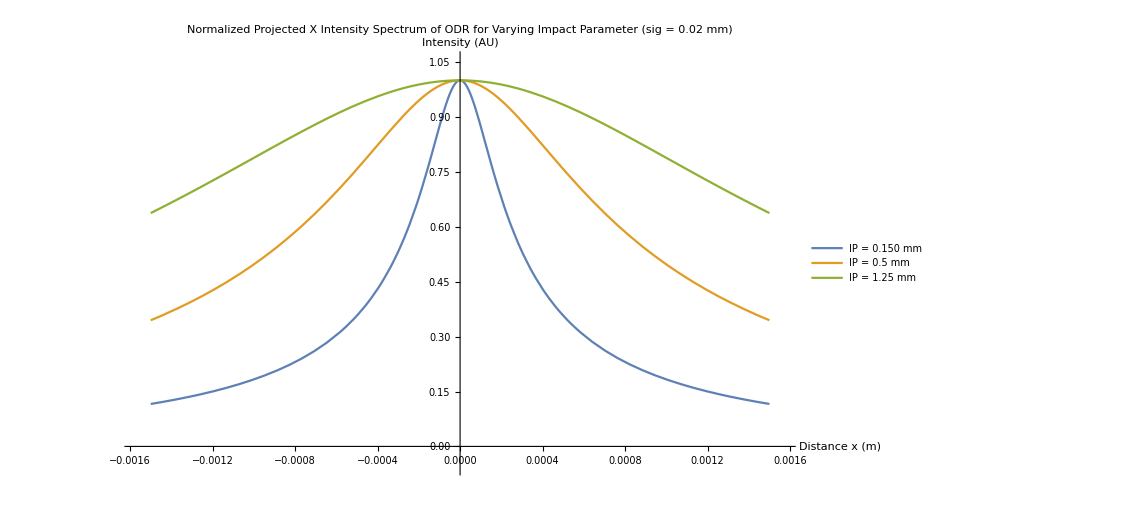

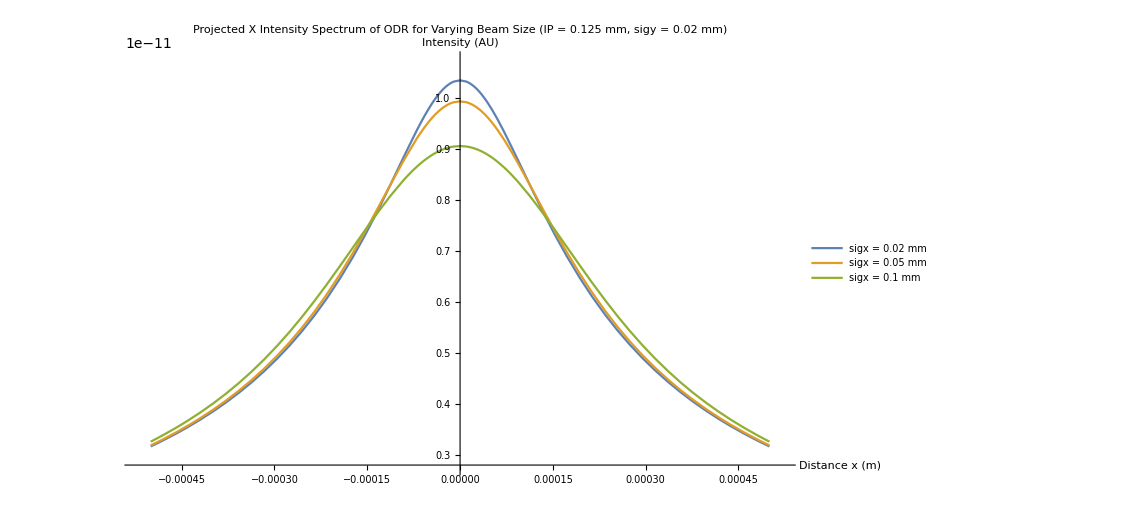

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NSolve::elemc: Unable to resolve the domain or region membership condition x ∈ x > 0.

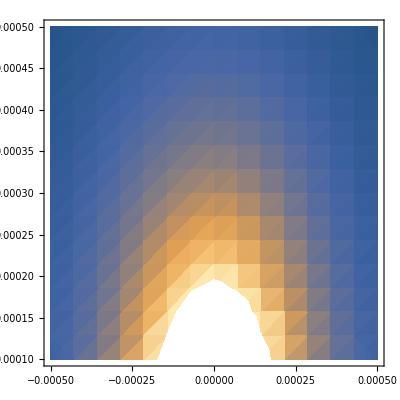
```mathematica
-Graphics-
NIntegrate[Intensity2[ux,uy,averagelambda],{ux,-500*^-6,500*^-6},{uy,130*^-6,500*^-6}]
```

-Graphics-

NIntegrate::inumr: The integrand 10000000000000000\ ⅇ^1/2\ (-2500000000\ x^2 - 2500000000\ y^2)\ BesselK[1, 50\ √Plus[« 2 »]^2 + Plus[« 2 »]^2]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3/25000, 3/25000}, {-3/25000, 3/25000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Throw::nocatch: Uncaught -Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x$144128] + SuperscriptBox[ returned to top level.

Throw::nocatch: Uncaught -(1 + NIntegrate`LevinRuleDump`x$144132^2) Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x$144132] + NIntegrate`LevinRuleDump`x$144132 SuperscriptBox[ returned to top level.

General::stop: Further output of Throw :: nocatch will be suppressed during this calculation.

Hold[Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x$144128]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x$144128],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x$144128]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x$144128],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-(1+(NIntegrate`LevinRuleDump`x$144132)^2) Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x$144132]+NIntegrate`LevinRuleDump`x$144132 Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x$144132]+(NIntegrate`LevinRuleDump`x$144132)^2 Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x$144132],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation]]